# Package Development

## Ian Johnson Wolfram Summer School 17

## Why Packages?

Way to distribute code to others

Organizes code in usable way for others

## Packages vs Notebooks

### Notebooks

Easy to use

Powerful graphics

Editable

Difficult to distribute

### Packages

Convenient to distribute

Easy to load

Abstract implementation from user

## Workflows

Package Editor in Mathematica

Wolfram Workbench + Eclipse

Other text editors - Sublime, TextMate, etc.

## Best practices

### Source control - Git, CVS, Mercurial, etc.

For git, there is a package for interfacing with git in Mathematica : https://github.com/WolframResearch/GitLink

### Unit testing - MUnit

https://www.youtube.com/watch?v=2jQl6Wj8CA8

Workbench tests

### Consistent, and minimal design

Have functions with take sensibly defaults

Strive to have the “automagic” case with minimal arguments

Examples:

```mathematica
CurrentImage[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

versus

```mathematica
ImageCapture[]
```

Then also have the full form of the function

Use documented Options to control methods, styles, etc.

```mathematica
myNewPlot[data_,opts:OptionsPattern[]]:=ListPlot[data,opts]
```

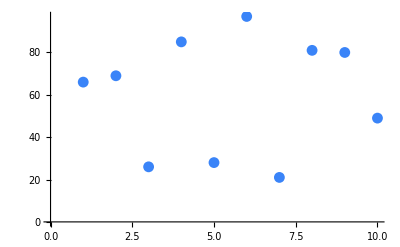

```mathematica
myNewPlot[RandomInteger[100,10]]
```

```mathematica
myNewPlot[RandomInteger[100,10],PlotTheme->"Marketing"]
```

-Graphics-

### Documentation

Source code documentation is a must

Notebooks are very useful for notebook purposes

DocuTools is an internal package we have for writing the documentation of the wolfram language

## Coding styles

### Modularize everything

As many sub-functions, etc. as makes sense

Makes easy to refactor/add functionality later

Makes it easy to write unit tests

```mathematica
2+2
```

```mathematica
Plus[2,2]
```

```mathematica
VerificationTest[Total[{2,2}]==4]
```

TestResultObject[…]

### Contexts / files

Separate into logical components

Shouldn’t have files that are like 6000 lines long

Better to have 6-12 files that are each themselves more readable

### Use multiple patterns for same functions

Much easier to follow the flow of functions

```mathematica
ClearAll[f];
ClearAll[f2]
```

```mathematica
f[x_?IntegerQ]:=x+2
```

```mathematica
f2[x_Integer]:=x+2
```

```mathematica
f[3]
```

5

```mathematica
f[Integer["not a integer"]]
```

f[Integer[not a integer]]

```mathematica
f2[Integer["not a integer"]]
```

2+Integer[not a integer]

```mathematica
f2[Integer["not a integer"]]
```

2+Integer[not a integer]

```mathematica
f[x:{_ Integer..}]/;AllTrue[IntegerQ]@x:=...
```

```mathematica
f[___]:=(Message[f::wrong];$Failed)
```

### Issue helpful and informative messages

Can write own messages as symbol::tag, issue with Message[...]

```mathematica
f::wrong="the input, `1`, to f is wrong, f expects an integer "
```

the input, `1`, to f is wrong, f expects an integer

```mathematica
Message[f::wrong,{1,2,3,5}]
```

f::wrong: the input, {1,2,3,5}, to f is wrong, f expects an integer

Usage messages can be nicely formatted nicely with the SetUsage function from GeneralUtilities` context

```mathematica
func::usage="func returns womthing"
```

func returns womthing

```mathematica
func[x_]:=x+423456
```

```mathematica
??func
```

func returns womthing

func[x_]:=x+423456

```mathematica
??System`*
```

```mathematica
<<GeneralUtilities`
SetUsage[func,"func[x$,y$, $$] computes x$1, x$2, $$, x$i given something."];
?func
```

RowBox[{"func", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",",  StyleBox["…", "TR"]}], "]"}] computes StyleBox[SubscriptBox["x", StyleBox["1", "TR"]], "TI"], StyleBox[SubscriptBox["x", StyleBox["2", "TR"]], "TI"], …, StyleBox[SubscriptBox["x", StyleBox["i", "TI"]], "TI"] given something.

This function also works with auto-complete with the parameters:

```mathematica
func[1,2,3]
```

func[1,2,3]

## Packages / Paclets

### Packages

Simple .m or .wl files

Simple straightforward to use, but cumbersome with many of files

### Paclets

#### “Official” way to implement packages and distribute

Many WL functions are implemented and maintained using paclets

#### Allows for unlimited files, organization, etc. all distributed in a single .paclet file

Bundles of package .wl files are difficult to distribute in groups

#### Is automatically update-able

Uses a versioning system

#### Can provide auto-loaded symbols

User doesn’t need to load or know about the package

#### Includes programmatic way to access external files like data files, images, etc.

```mathematica
ImageResize[Import@PacletResource["ExternalEvaluate","PythonIcon"],100]
```

-Graphics-

```mathematica
Short[Import[PacletResource["DeviceDriver_Arduino","Sketch"],"Text"],3]
```

/*SketchTemplate.cpp*/

/*file that is uploaded to the Arduino Uno*/

/*Author: Ian Johnson, Wolfram R…eduledQueue));
		}/*end else block for no SerialLink.available()*/
      }/*end infinite while loop*/
}

#### Workbench can generate the layout for you

```mathematica
Dataset@FileSystemMap[Hyperlink[FileNameTake[#],#]&,Lookup[PacletInformation["ZeroMQLink"],"Location"],Infinity]
```

Dataset[<>]

#### Inspect-able by users

```mathematica
Dataset@Association@PacletInformation["ZeroMQLink"]
```

Dataset[<>]

## Example walkthrough with Workbench + GitHub